```mathematica
(*This mathematica script produces figure 11 of arXiv:2306.03893.*)
(*NB: All the equation numbers come from arXiv:2306.03893*)
(*NB: These scripts produces some computational errors. These are because of the breakdown of numercial methods (e.g. NIntegrate) in the unphysical region and the lack of precise test to exclude them. Therrefore, it does not influence the physical results of the paper.*)
```

## DATA SCAN

```mathematica
DATAPlus = {{mt0->170.,Yt0->0.9177046844595703,λ0->0.005537840016814139,b->0.000022261406949712544,q->0.33840663368217183,ξcent->0.07660000000000002},{mt0->170.25,Yt0->0.9191638473923207,λ0->0.00395130850979683,b->0.00002273980608174033,q->0.34337846047769355,ξcent->0.09446},{mt0->170.5602,Yt0->0.9209744064390496,λ0->0.0019753119183642935,b->0.00002336551563439747,q->0.344972724155993,ξcent->0.07338},{mt0->170.6,Yt0->0.9212067112846968,λ0->0.0017217032099142652,b->0.000023418201406264023,q->0.34498698251211446,ξcent->0.08644}};
DATAMinus = {{mt0->171.661,Yt0->0.9273997383774291,λ0->-0.0050977826819124565,b->0.00002556396958439446,q->0.3170293840528272,ξcent->0.1276},{mt0->172.16,Yt0->0.930312493141963,λ0->-0.008346158824433627,b->0.000027169241101022356,q->0.28937789156163557,ξcent->0.17770000000000002},{mt0->172.46,Yt0->0.9320636766089252,λ0->-0.010303203995950617,b->0.00002780533995579692,q->0.272439096210283,ξcent->0.237},{mt0->172.6,Yt0->0.9328809005896119,λ0->-0.011213190826425508,b->0.000027760671675281775,q->0.26528468035699865,ξcent->0.216},{mt0->172.76,Yt0->0.9338148657541936,λ0->-0.012267716676254729,b->0.00002844665271177031,q->0.2545115831381372,ξcent->0.2085},{mt0->173.06,Yt0->0.9355660704506669,λ0->-0.014239787244079621,b->0.000029092817425828582,q->0.23605709527641422,ξcent->0.188},{mt0->173.35999999999999,Yt0->0.9373173170889816,λ0->-0.016219516738449027,b->0.000029743470153224285,q->0.217479262009232,ξcent->0.171346},{mt0->173.6,Yt0->0.938718,λ0->-0.0178169,b->0.0000307375,q->0.201917,ξcent->0.17500000000000002},{mt0->174.,Yt0->0.9410541461003352,λ0->-0.020477396117170123,b->0.00003163143902656302,q->0.17851594474528537,ξcent->0.16600000000000004}};
```

## SCAN POSITIVE

```mathematica
DATp = {};
DATpEnh={};
For[ψ=1,ψ<=Length[DATAPlus],ψ++,
(*Extraction of parameters*)
Clear[λ0,q,b,ξcent];
FitParam = DATAPlus[[ψ]];

Yt0 = Yt0/.FitParam[[2]];
λ0 = λ0/.FitParam[[3]];b = b/.FitParam[[4]];q = q/.FitParam[[5]];yt = 0.42733042003306865;ξcent = ξcent/.FitParam[[6]];
(*Script for the negative λ0: reproduces the datas for the 4 panels of figure 8.*)
(*I. Definitions*)
ξlow=ξcent-9 10^(-4); ξup=ξcent+9 10^(-4); Size =20;(*Scan Range/Size*)
xi[p1_]:= ξlow + (ξup-ξlow)(p1/Size);
Dat = {}; CMB = {}; Lam = {}; Init = {};
(*Functions of the theory*)
F[x1_,ξ1_]= (1/Sqrt[ξ1])Tanh[Sqrt[ξ1]x1];(*Palatini F, eq (3.11)*)
λSM[μ1_]= λ0 + b Log[μ1/q]^2;(*Sm Running Without UV as function of the scale μ, eq (3.22)*)
μ[x1_,ξ1_]= yt F[x1,ξ1];(*Energy Scale as the top mass eq (3.26)*)
G[x1_,ξ1_]=(D[F[x1,ξ1],x1])^2 + (1/3)(D[D[F[x1,ξ1],x1],x1])F[x1,ξ1];(*Definition of the jump function according to 1412.3811 paper, eq (3.30)*)
λ[x1_,ξ1_,δλ1_]= λSM[μ[x1,ξ1]]+ δλ1(1-G[x1,ξ1]^2);(*UV Running, eq (3.28)*)
U[x1_,ξ1_,δλ1_]= (1/4)λ[x1,ξ1,δλ1]F[x1,ξ1]^4;(*Full Potential, eq (3.31)*)
dU[x1_,ξ1_,δλ1_]=( D[U[x1,ξ1,δλ1],x1]);(*We take the derivative of the potential in order to use it later.*)
ϵSR[x1_,ξ1_,δλ1_]= 1/2(dU[x1,ξ1,δλ1]/U[x1,ξ1,δλ1])^2;(*Slow roll parameter in order to define initial conditions for the velocity.*)
δλmin[ξ1_]=-λ0-b Log[yt/(q Sqrt[ξ1])]^2 ;(*Minimal value of the jump such that the potential and its derivative stay positive at large field, eq (4.33)*)
(*II. Scan over ξ*)
For[p=Size, p>=0, p--, ξ = xi[p];
(*II.A. According to the procedure described in section 4.2.2, we find the allowed interval for δλ at given ξ.*)
(*II.A.1. We find the upper bound δλplus*)
δup = λ0+0.0001; δlow = Abs[δλmin[ξ]]/1000; Nstep = 30;
Pos = False;
Firs = 0;
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
L = Length[Rank];
If[L!=0,If[U[dUTab[[Rank[[L]]]][[1]],ξ,δλ]>0,Pos = True]];
If[Firs == 0, If[L==0, R = i; Firs = 1]];

];
δplus = δlow (δup/δlow)^((R-1)/(Nstep-1));
δλplus = δλmin[ξ]+δplus;
(*II.A.2 We find the lower bound δλminus*)
Nstep = 30;
Test = False;
n = 1;
While[Test ==False && n<=Nstep,
δminus = δlow (δplus/δlow)^((n-1)/(Nstep-1));
δλ = δλmin[ξ]+δminus;
TU = Table[U[x,ξ,δλ],{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
TX = Table[x,{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
MaxU = Max[TU];
If[MaxU==U[ TX[[Length[TX]]],ξ,δλ],Test = True, Test = False];
n= n+1;
](*PositiveNess*);
If[Min[TU]<0,Pos = False;,Pos = True;];
n = 1;
Firs = 0;
δmin = δminus;
While[Pos == False && n<=Nstep,
δ = δmin(δplus/δmin)^((n-1)/(Nstep-1));
δλ =  δλmin[ξ]+δ;
TU = Table[U[x,ξ,δλ],{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
If[Min[TU]>0,Pos = True];
If[Firs==0, If[Pos==True,δminus = δ; Firs=1]];
n=n+1
];
δλminus = δλ;
ClearAll[δλ];
(*II.B. Scan Over δλ € [δλminus,δλplus] in order to find the minimal initial power spectrum.*)
nSize = 100;
δλ[n1_]= δλminus + (n1/nSize)(δλplus - δλminus)(*Parametrizes the Jump between the two bounds. n =100 corresponds to the smallest loc min and 0 to the largest.*);
(*Finds the largest n such that the inflation is still ending somewhere*)
Fin = True;Hilltop = False; n=nSize; L = 1000/Sqrt[ξ]; χi = 4/Sqrt[ξ]; PCMBn = {};Enhn={};NoInf=False;
While[Fin == True && n>=0 && Hilltop == False,
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)(dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]])==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= (1/2)(χsol'[x1])^2;
(*ANOTHER FACTOR OF 2 WAS MISSING HERE*)
H[x1_]=Sqrt[2 U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
If[Max[Table[Re[ϵ[x]],{x,0,Nup,Nup/10000}]]>=1,
Fin = True;,(*Inflation comes to an end for this value of n.*)
Fin = False; nMin = n+1(*Inflation does not come to an end for this n, the minimal n in n+1..*);If[n==nSize, NoInf=True;](*If the inflation does not ends for the largest n, this is not a good value of ξ to consider.*);];
(*When Inflation is ending, it happens sometimes that the inflation begins at the left of the local maximum, preventing the system to go through the required USR phase. The aim of this test is to avoid these cases.*)
(*a) We find the value of Nend and NCMB.*)
If[Fin==True,
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
(*b) We find the location of the local maximum, i.e. the first time that the derivative chanhge its sign.*)
dUTab = Table[{dU[x,ξ,δλ[n]],x},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}];
Passed = False;
For[k = 1,k<=Length[dUTab]-1,k++, 
If[Sign[dUTab[[k]][[1]]]!= Sign[dUTab[[k+1]][[1]]],Passed = True; χex = dUTab[[k]][[2]];Break[]];
];
If[Passed == False, 
MinDer = Min[ Table[{dU[x,ξ,δλ[n]]},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}]];
For[k = 1,k<=Length[dUTab]-1,k++, 
If[dUTab[[k]][[1]]==MinDer, χex = dUTab[[k]][[2]]]
];
];
(*c. Now we compare a and b.*)
If[Re[χsol[NCMB]]<= χex,Hilltop = True; nMin = n+1; If[n==nSize, NoInf==True(*If Hilltop = True at n=nSize, this mean that it is an unavoidable scenario for these (λ0,ξ)*);],Hilltop = False; 
(*!!!!!!!!!!!!!!!!!*) 
Mp = 2.4 10^18;(*GeV*);
HMpc[x1_] = H[x1] Mp 1.56 10^38; (*Mpc^-1*);
ascale[Nfold_]=(0.05 (*Mpc^-1*)/( HMpc[NCMB](*Mpc^-1*))) Exp[Nfold-NCMB];
L1 = 10;
kcross[Nfold_]= (0.05/H[NCMB])H[Nfold]E^(Nfold-NCMB);
Ncross = Interpolation[Table[{Re[kcross[x]],x},{x,NCMB-5,Nend,0.01}]];
k = kcross[NCMB];
ki = k/L1;(*we define some scale that crosses the Hubble radius when k is still in the BD vacuum. Here, ki crosses 1 efold before the CMB.*)
Ni = Ncross[ki];(*Initial time for Mukhanov Sasaki intergation*)
Nf = Ncross[NCMB]+5;
η[x1_] = ϵ[x1] - 0.5 ϵ'[x1]/ϵ[x1];
Scaling = 10^6;
Foo[x1_,k1_] = (k1/(kcross[x1]))^2+(1+ϵ[x1] - η[x1])(η[x1]-2)-(ϵ'[x1]-η'[x1]);
Ruin = 1/Scaling; dRuin = 0;(*Real Part of Bunch Davies Vacuum*)
Rusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Ruin,f'[Ni]==dRuin},f,{x,Ni,Nf}];(*Real Part of MS*)
Iuin = 0; dIuin = -k/ki/Scaling;(*Imaginary part of Bunch Davies Vacuum*)
Iusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Iuin,f'[Ni]==dIuin},f,{x,Ni,Nf}];(*Imaginary part of MS*)
uSquared = Scaling^2/(2 k)(Rusol[Nf]^2 + Iusol[Nf]^2); (*Mpc, since we set the initial condition as fct of k in Mpc*)
z = -ascale[Nf]χsol'[Nf] Mp 1.56 10^38; (*Mpc^-1, the numerical factor is the conversion factor btw Mpc^-1 and GeV.*)
Pow = k^3 uSquared/((2π^2)z^2);(*Dimensionless*)
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
(*!!!!!!!!!!!!!!!!!*) 
AppendTo[PCMBn,{n,Pow(*H[NCMB]^2/(8 Pi^2 ϵ[NCMB])*)}];
AppendTo[Enhn,{n,Enh}];
(*We keep the SR CMB in memeory for each n.*)n = n-1;];];
](*End of the scan over δλ*);
(*We select the minimal CMB and we make all the standard dynamics.*)
PCMBnValues ={};
For[i=1,i<=Length[PCMBn], i++, AppendTo[PCMBnValues,{PCMBn[[i]][[2]]}]];
CMBnMin = Min[PCMBnValues];ClearAll[PCMBnValues];
For[i=1, i<=Length[PCMBn], i++,If[PCMBn[[i]][[2]]==CMBnMin, Rankn = i]];
nMinCMB = PCMBn[[Rankn]][[1]];
(*(*We re do the analysis for the minimal CMB*)
If[NoInf==False,
n = nMinCMB;
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)(dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]])==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= (1/2)(χsol'[x1])^2;
(*ANOTHER FACTOR OF 2 WAS MISSING HERE*)
H[x1_]=Sqrt[2 U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
AppendTo[Dat,{ξ,Enh[[nMinCMB]][[2]]}];
AppendTo[CMB,{ξ,PCMBn[[nMinCMB]][[2]]}];
AppendTo[Lam,{ξ,δλ[n]}];
AppendTo[Init,{ξ,χsol[NCMB]}];
];*)
AppendTo[Dat,{ξ,Enhn[[Rankn]][[2]]}];
AppendTo[CMB,{ξ,PCMBn[[Rankn]][[2]]}];
](*End of the loop over ξ*);
AppendTo[DATp,{Yt0,Min[CMB]}];
AppendTo[DATpEnh,{Yt0,Max[Dat]}];
Print["ψ="ψ];
];
(*(*III. We compute the exact Power Spectrum.*)
ExCMB = {};
For[i=1, i<=Length[CMB],i++,
ξ = CMB[[i]][[1]]; δλ = Lam[[i]][[2]];χi =4/Sqrt[ξ]; L = 1000;Enh = Dat[[i]][[2]];
dχi = -Sqrt[2ϵSR[χi,ξ,δλ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)(dU[y[Ne],ξ,δλ]/U[y[Ne],ξ,δλ])==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= (1/2)(χsol'[x1])^2;
(*ANOTHER FACTOR OF 2 WAS MISSING HERE*)
H[x1_]=Sqrt[2 U[χsol[x1],ξ,δλ]/(6-(χsol'[x1])^2)];
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[j=2,j<10,j++, Nup1 = Nup/j;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(j-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Mp = 2.4 10^18;(*GeV*);
HMpc[x1_] = H[x1] Mp 1.56 10^38; (*Mpc^-1*);
ascale[Nfold_]=(0.05 (*Mpc^-1*)/( HMpc[NCMB](*Mpc^-1*))) Exp[Nfold-NCMB]; ;
L1 = 10;
kcross[Nfold_]= (0.05/H[NCMB])H[Nfold]E^(Nfold-NCMB);
Ncross = Interpolation[Table[{Re[kcross[x]],x},{x,NCMB-5,Nend,0.01}]];
k = kcross[NCMB];
ki = k/L1;(*we define some scale that crosses the Hubble radius when k is still in the BD vacuum. Here, ki crosses 1 efold before the CMB.*)
Ni = Ncross[ki];(*Initial time for Mukhanov Sasaki intergation*)
Nf = Ncross[NCMB]+5;
η[x1_] = ϵ[x1] - 0.5 ϵ'[x1]/ϵ[x1];
Scaling = 10^6;
Foo[x1_,k1_] = (k1/(kcross[x1]))^2+(1+ϵ[x1] - η[x1])(η[x1]-2)-(ϵ'[x1]-η'[x1]);
Ruin = 1/Scaling; dRuin = 0;(*Real Part of Bunch Davies Vacuum*)
Rusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Ruin,f'[Ni]==dRuin},f,{x,Ni,Nf}];(*Real Part of MS*)
Iuin = 0; dIuin = -k/ki/Scaling;(*Imaginary part of Bunch Davies Vacuum*)
Iusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Iuin,f'[Ni]==dIuin},f,{x,Ni,Nf}];(*Imaginary part of MS*)
uSquared = Scaling^2/(2 k)(Rusol[Nf]^2 + Iusol[Nf]^2); (*Mpc, since we set the initial condition as fct of k in Mpc*)
z = -ascale[Nf]χsol'[Nf] Mp 1.56 10^38; (*Mpc^-1, the numerical factor is the conversion factor btw Mpc^-1 and GeV.*)
Pow = k^3 uSquared/((2π^2)z^2);(*Dimensionless*)
AppendTo[ExCMB,{ξ,Pow}];

];
(*Finds the Minimal CMB using MS.*)
ExCMBValues = {};
For[i=1,i<=Length[ExCMB],i++, AppendTo[ExCMBValues,ExCMB[[i]][[2]]]];
MinExCMBValues = Min[ExCMBValues];
AppendTo[DATp,{Yt0,MinExCMBValues}];
AppendTo[DATpEnh,{Yt0,Enh}];
Print["ψ="ψ];
]*)
```

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1199.38.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1200.23.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1201.3.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

ψ=

General::munfl: -5.95127×10^-298 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.19373×10^-298 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.92473×10^-300 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

2 ψ=

3 ψ=

NDSolveValue::ndsz: At Ne == 1043.59, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At Ne == 1101.38, step size is effectively zero; singularity or stiff system suspected.

4 ψ=

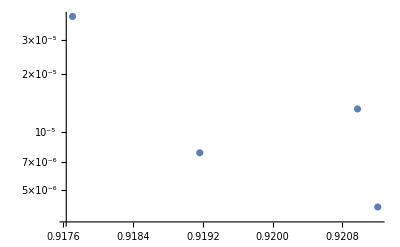

```mathematica
ListLogPlot[DATp]
```

```mathematica
DATp
```

{{0.917705,0.0000396001+0. ⅈ},{0.919164,7.77056×10^-6+0. ⅈ},{0.920974,0.0000131199+0. ⅈ},{0.921207,4.06665×10^-6+0. ⅈ}}

## SCAN NEGATIVE

```mathematica
DATm = {};
DATmEnh={};
For[ψ=1,ψ<=Length[DATAMinus],ψ++,
(*Extraction of parameters*)
ClearAll[λ0,q,b,ξcent];
FitParam = DATAMinus[[ψ]];

Yt0 = Yt0/.FitParam[[2]];
λ0 = λ0/.FitParam[[3]];b = b/.FitParam[[4]];q = q/.FitParam[[5]];yt = 0.42733042003306865;ξcentral = ξcent/.FitParam[[6]];
(*Script for the negative λ0: reproduces the datas for the 4 panels of figure 8.*)
(*I. Definitions*)
ξlow=ξcentral- 10^(-2); ξup=ξcentral+ 10^(-2); Size =100;(*Scan Range/Size*)
xi[p1_]:= ξlow + (ξup-ξlow)p1/Size;
(*Table where we will put all the values of the scan*)
Dat = {}; CMB = {}; 
(*Functions of the theory*)
F[x1_,ξ1_]= 1/Sqrt[ξ1] Tanh[Sqrt[ξ1]x1];(*Palatini F, eq (3.11)*)
λSM[μ1_]= λ0 + b Log[μ1/q]^2;(*Sm Running Without UV as function of the scale μ, eq (3.22)*)
μ[x1_,ξ1_]= yt F[x1,ξ1];(*Energy Scale as the top mass eq (3.26)*)
G[x1_,ξ1_]=(D[F[x1,ξ1],x1])^2 + 1/3(D[D[F[x1,ξ1],x1],x1])F[x1,ξ1];(*Definition of the jump in the coupling constant according to 1412.3811, eq (3.29)*)
λ[x1_,ξ1_,δλ1_]= λSM[μ[x1,ξ1]]+ δλ1(1-G[x1,ξ1]^2);(*UV Running, eq (3.28)*)
U[x1_,ξ1_,δλ1_]= 1/4 λ[x1,ξ1,δλ1]F[x1,ξ1]^4;(*Full Potential, eq (3.31)*)
dU[x1_,ξ1_,δλ1_]=( D[U[x1,ξ1,δλ1],x1]);(*We take the derivative of the potential in order to use it later.*)
ϵSR[x1_,ξ1_,δλ1_]= 1/2(dU[x1,ξ1,δλ1]/U[x1,ξ1,δλ1])^2;(*Slow roll parameter in order to define initial conditions for the velocity as function of the initial condition.*)
δλmin[ξ1_]=-λ0-b Log[yt/(q Sqrt[ξ1])]^2 ;(*Minimal value of the jump such that the potential and its derivative stay positive at large field, eq (4.30)*)
(*II. Scan over ξ.*)
For[p=Size,p>=0, p--, ξ = xi[p];
(*II.A. According to the procedure described in section 4.2.2, we find the allowed interval for δλ at given ξ.*)
(*II.A.1. We find the upper bound δλplus*)
δup = Abs[λ0]; δlow = δλmin[ξ]/1000; Nstep = 30;
Module[{δ,dUTab,Rank,Test,Firs},
Pos = False;
Firs = 0;
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
If[U[dUTab[[Rank[[Length[Rank]]]]][[1]],ξ,δλ]>0,Pos = True];
If[Firs == 0, If[Length[Rank]!=4, R = i; Firs = 1]];

];
δplus = δlow (δup/δlow)^((R-1)/(Nstep-1));];
δλplus = δλmin[ξ]+δplus;
(*II.A.2 We find the lower bound δλminus*)
(*NB: Sometimes, at δλplus, the almost inflection point is still negative. In these cases, there is no way to find a local min in the potential. Hence, the program sets Pos==False which stops the loop on p.*)
If[Pos == True,δup = δplus; δlow = 10^(-6)δλmin[ξ]; Nstep = 50;
Module[{Rank2,δ,dUTab,Rank,Test,ULocMin,Neg},
Rank2 = {};
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
ULocMin = U[dUTab[[Rank[[Length[Rank]]]]][[1]],ξ,δλ];
If[ULocMin >=0, Neg = False,Neg = True];
If[Neg == False,AppendTo[Rank2,i]]
];
δminus  = δlow (δup/δlow)^(Rank2[[1]]/Nstep);
δλminus =δλmin[ξ]+δminus;],Break[](*Stops the scan if Pos==False because we reach the lower bound on ξ.*)];
ClearAll[δλ];
(*II.B. Scan Over δλ € [δλminus,δλplus] in order to find the minimal initial power spectrum.*)
nSize = 100;
δλ[n1_]= δλminus + n1/nSize(δλplus - δλminus)(*Parametrizes the Jump between the two bounds. n =100 corresponds to the smallest loc min and 0 to the largest.*);
(*Finds the largest n such that the inflation is still ending somewhere*)
Fin = True;Stable = True;Hilltop = False; n=nSize; L = 1000/Sqrt[ξ]; χi = 4/Sqrt[ξ]; PCMBn = {};Enhn={};
While[Fin == True && n>=0 && Hilltop == False && Stable == True,
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[2U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
If[Max[Table[Re[ϵ[x]],{x,0,Nup,Nup/10000}]]>=1,
Fin = True;,(*Inflation comes to an end for this value of n.*)
Fin = False; nMin = n+1(*Inflation does not come to an end for this n, the minimal n in n+1..*);];
(*If the inflation does not ends for the largest n, this is not a good value of ξ to consider.*)
If[Fin==False && n==nSize,NoInf=True,NoInf=False];
If[Fin==True, (*When Inflation is ending, it happens sometimes that the inflation begins at the left of the local maximum, preventing the system to go through the required USR phase. The aim of this test is to avoid these cases.*)
(*a) We find the value of Nend and NCMB.*)
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; If[ϵ[Nup/i]<1,Ninf = Nup /i,Ninf = Nup1/2];
, Ninf = Nup/2; Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
(*b) We find the location of the local maximum, i.e. the first time that the derivative chanhge its sign.*)
dUTab = Table[{dU[x,ξ,δλ[n]],x},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}];
Passed = False;
For[k = 1,k<=Length[dUTab]-1,k++, 
If[Sign[dUTab[[k]][[1]]]!= Sign[dUTab[[k+1]][[1]]],Passed = True; χex = dUTab[[k]][[2]];Break[]];
];
If[Passed == False, 
MinDer = Min[ Table[{dU[x,ξ,δλ[n]]},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}]];
For[k = 1,k<=Length[dUTab]-1,k++, 
If[dUTab[[k]][[1]]==MinDer, χex = dUTab[[k]][[2]]]
];
];
(*c. Now we compare a and b.*)
If[Re[χsol[NCMB]]<= χex,Hilltop = True; nMin = n+1;,Hilltop = False;];
];
(*If Hilltop = True at n=nSize, this mean that it is an unavoidable scenario for these (λ0,ξ)*)
If[Hilltop==True && n==nSize, NoInf==True;,NoInf==False;];
If[Fin == True && Hilltop == False,
χStable = Interpolation[Table[{U[x,ξ,δλ[n]],x},{x,0.5/Sqrt[ξ],4/Sqrt[ξ],0.01/Sqrt[ξ]}]][0];
(*If the previous test is concluding, we still have to make a stability test due to the negative λ0*)
If[χsol[Nend]<=χStable, Stable = False; nMin = n+1; , Stable = True; 
(*!!!!!!!!!!!!!!!!!!!!!!!!!!*)
Mp = 2.4 10^18;(*GeV*);
HMpc[x1_] = H[x1] Mp 1.56 10^38; (*Mpc^-1*);
ascale[Nfold_]=(0.05 (*Mpc^-1*)/( HMpc[NCMB](*Mpc^-1*))) Exp[Nfold-NCMB];
L1 = 10;
kcross[Nfold_]= (0.05/H[NCMB])H[Nfold]E^(Nfold-NCMB);
Ncross = Interpolation[Table[{Re[kcross[x]],x},{x,NCMB-5,Nend,0.01}]];
k = kcross[NCMB];
ki = k/L1;(*we define some scale that crosses the Hubble radius when k is still in the BD vacuum. Here, ki crosses 1 efold before the CMB.*)
Ni = Ncross[ki];(*Initial time for Mukhanov Sasaki intergation*)
Nf = Ncross[NCMB]+5;
η[x1_] = ϵ[x1] - 0.5 ϵ'[x1]/ϵ[x1];
Scaling = 10^6;
Foo[x1_,k1_] = (k1/(kcross[x1]))^2+(1+ϵ[x1] - η[x1])(η[x1]-2)-(ϵ'[x1]-η'[x1]);
Ruin = 1/Scaling; dRuin = 0;(*Real Part of Bunch Davies Vacuum*)
Rusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Ruin,f'[Ni]==dRuin},f,{x,Ni,Nf}];(*Real Part of MS*)
Iuin = 0; dIuin = -k/ki/Scaling;(*Imaginary part of Bunch Davies Vacuum*)
Iusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Iuin,f'[Ni]==dIuin},f,{x,Ni,Nf}];(*Imaginary part of MS*)
uSquared = Scaling^2/(2 k)(Rusol[Nf]^2 + Iusol[Nf]^2); (*Mpc, since we set the initial condition as fct of k in Mpc*)
z = -ascale[Nf]χsol'[Nf] Mp 1.56 10^38; (*Mpc^-1, the numerical factor is the conversion factor btw Mpc^-1 and GeV.*)
Pow = k^3 uSquared/((2π^2)z^2);(*Dimensionless*)
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
(*!!!!!!!!!!!!!!!!!!!!!!!!!!*)
AppendTo[PCMBn,{n,Pow}];
AppendTo[Enhn,{n,Enh}];
 n = n-1;];
If[Stable ==False && n==100, NoInf == True;,NoInf==False];
];
];
(*End of the scan over the jump.*)
If[n==100,If[Fin==False,NoInf = True;,NoInf = False;],NoInf=False;]
(*II.C. We select the minimal CMB*);
PCMBnValues ={};
For[i=1,i<=Length[PCMBn], i++, AppendTo[PCMBnValues,{PCMBn[[i]][[2]]}]];
CMBnMin = Min[PCMBnValues];ClearAll[PCMBnValues];
For[i=1, i<=Length[PCMBn], i++,If[PCMBn[[i]][[2]]==CMBnMin, Rankn = i]];
nMinCMB = PCMBn[[Rankn]][[1]];
AppendTo[Dat,{ξ,Enhn[[Rankn]][[2]]}];
AppendTo[CMB,{ξ,PCMBn[[Rankn]][[2]]}];
](*End of scan over ξ*);
AppendTo[DATm,{Yt0,Min[CMB]}];
AppendTo[DATmEnh,{Yt0,Max[Dat]}];
Print["ψ="ψ];
](*End of Scan Over ψ*)
```

NDSolveValue::ndsz: At Ne == 518.797, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At Ne == 519.358, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At Ne == 519.923, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

ψ=

2 ψ=

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {-2.44949,ComplexInfinity} is not a list of numbers with dimensions {2} at {Ne,y[Ne],y'[Ne]} = {315.744,1.68009,-2.44949}.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {-2.44949,ComplexInfinity} is not a list of numbers with dimensions {2} at {Ne,y[Ne],y'[Ne]} = {315.992,1.68078,-2.44949}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {-2.44949,ComplexInfinity} is not a list of numbers with dimensions {2} at {Ne,y[Ne],y'[Ne]} = {316.737,1.68287,-2.44949}.

General::stop: Further output of NDSolveValue::nlnum will be suppressed during this calculation.

3 ψ=

InterpolatingFunction::dmval: Input value {360.206} lies outside the range of data in the interpolating function. Extrapolation will be used.

4 ψ=

InterpolatingFunction::dmval: Input value {372.136} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

5 ψ=

6 ψ=

7 ψ=

8 ψ=

9 ψ=

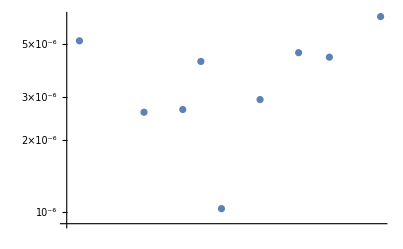

```mathematica
ListLogLogPlot[DATm]
```

```mathematica
DAT=DATp;
For[i=1,i<=Length[DATm],i++,AppendTo[DAT,{DATm[[i]][[1]],DATm[[i]][[2]]}]];
DATENH = DATpEnh;
For[i=1,i<=Length[DATmEnh],i++,AppendTo[DATENH,{DATmEnh[[i]][[1]],DATmEnh[[i]][[2]]}]];
```

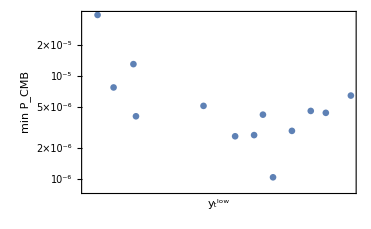

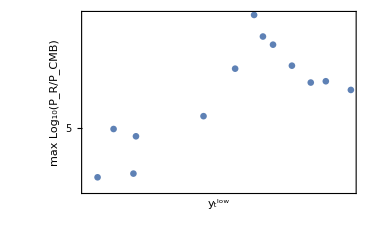

```mathematica
ListLogLogPlot[DAT,Frame->True,FrameStyle->Black,FrameLabel->{Superscript[Subscript["y",t],low],min Subscript[P,"CMB"]}]
ListLogLogPlot[DATENH,Frame->True,FrameStyle->Black,FrameLabel->{Superscript[Subscript["y",t],low],max Subscript[Log,10][Subscript[P,"R"]/Subscript[P,"CMB"]]}]
```

```mathematica
DAT
```

{{0.917705,0.0000396001+0. ⅈ},{0.919164,7.77056×10^-6+0. ⅈ},{0.920974,0.0000131199+0. ⅈ},{0.921207,4.06665×10^-6+0. ⅈ},{0.9274,5.13729×10^-6},{0.930312,2.5958×10^-6},{0.932064,2.66459×10^-6},{0.932881,4.21787×10^-6},{0.933815,1.03268×10^-6},{0.935566,2.93×10^-6},{0.937317,4.58635×10^-6},{0.938718,4.39405×10^-6},{0.941054,6.4763×10^-6}}

```mathematica
DATENH
```

{{0.917705,4.62035},{0.919164,4.98907},{0.920974,4.64764},{0.921207,4.93165},{0.9274,5.09199},{0.930312,5.4915},{0.932064,5.98113},{0.932881,5.77948},{0.933815,5.70507},{0.935566,5.51772},{0.937317,5.37158},{0.938718,5.38277},{0.941054,5.30884}}